```mathematica
inner3D := 2 Pi Integrate[Exp[-2 Pi I k r Cos[θ]]*Sin[θ],{θ,0,Pi}]
```

```mathematica
G=Limit[Assuming[{b>0, k>0},Integrate[Exp[-b r]/r inner3D r^2, {r,0,Infinity}]],b->0]
```

1/(k^2 π)

```mathematica
s[n_]:=Apart[(-d)^n D[1/Sqrt[r^2+a^2],{a,n}]/n!/.a->d,r]
```

```mathematica
s2[n_]:=Apart[(-d)^n D[(r^2+3/2a^2)/(r^2+a^2)^(3/2),{a,n}]/n!/.a->d,r]
```

```mathematica
FT[x_]:=Assuming[{d>0, k>0},Integrate[x inner3D r^2 ,{r,0,Infinity}]]
```

```mathematica
Fs[n_]:=Total[FT[Coefficient[s[n],d,Range[2n]]]*d^Range[2n]]
```

```mathematica
Fs2[n_]:=Total[FT[Coefficient[s2[n],d,Range[2n+2]]]*d^Range[2n+2]]
```

```mathematica
fs0 = ft3d1/.a->d
```

(2 d BesselK[1,2 d k π])/k

```mathematica
fs1=Fs[1]
```

4 d^2 π BesselK[0,2 d k π]

```mathematica
fs2=Fs[2]
```

-2 d^2 π BesselK[0,2 d k π]+4 d^3 k π^2 BesselK[1,2 d k π]

```mathematica
fs3=Fs[3]
```

-4 d^3 k π^2 BesselK[1,2 d k π]+8/3 d^4 k^2 π^3 BesselK[2,2 d k π]

```mathematica
fs4=Fs[4]
```

d^3 k π^2 BesselK[1,2 d k π]-4 d^4 k^2 π^3 BesselK[2,2 d k π]+4/3 d^5 k^3 π^4 BesselK[3,2 d k π]

```mathematica
fs5=Fs[5]
```

2 d^4 k^2 π^3 BesselK[2,2 d k π]-8/3 d^5 k^3 π^4 BesselK[3,2 d k π]+8/15 d^6 k^4 π^5 BesselK[4,2 d k π]

```mathematica
fs20=ft3d4/.a->d
```

2 d^2 π BesselK[2,2 d k π]

```mathematica
fs21=Fs2[1]
```

4 d^3 k π^2 BesselK[1,2 d k π]

```mathematica
fs22=Fs2[2]
```

-6 d^3 k π^2 BesselK[1,2 d k π]+4 d^4 k^2 π^3 BesselK[2,2 d k π]

```mathematica
fs23=Fs2[3]
```

4 d^3 k π^2 BesselK[1,2 d k π]-28/3 d^4 k^2 π^3 BesselK[2,2 d k π]+8/3 d^5 k^3 π^4 BesselK[3,2 d k π]

```mathematica
fs24=Fs2[4]
```

-d^3 k π^2 BesselK[1,2 d k π]+9 d^4 k^2 π^3 BesselK[2,2 d k π]-8 d^5 k^3 π^4 BesselK[3,2 d k π]+4/3 d^6 k^4 π^5 BesselK[4,2 d k π]

```mathematica
fs25=Fs2[5]
```

-4 d^4 k^2 π^3 BesselK[2,2 d k π]+10 d^5 k^3 π^4 BesselK[3,2 d k π]-24/5 d^6 k^4 π^5 BesselK[4,2 d k π]+8/15 d^7 k^5 π^6 BesselK[5,2 d k π]

```mathematica
T=Accumulate[{fs0,fs1,fs2,fs3,fs4,fs5}]
```

{(2 d BesselK[1,2 d k π])/k,4 d^2 π BesselK[0,2 d k π]+(2 d BesselK[1,2 d k π])/k,2 d^2 π BesselK[0,2 d k π]+(2 d BesselK[1,2 d k π])/k+4 d^3 k π^2 BesselK[1,2 d k π],2 d^2 π BesselK[0,2 d k π]+(2 d BesselK[1,2 d k π])/k+8/3 d^4 k^2 π^3 BesselK[2,2 d k π],2 d^2 π BesselK[0,2 d k π]+(2 d BesselK[1,2 d k π])/k+d^3 k π^2 BesselK[1,2 d k π]-4/3 d^4 k^2 π^3 BesselK[2,2 d k π]+4/3 d^5 k^3 π^4 BesselK[3,2 d k π],fs5+2 d^2 π BesselK[0,2 d k π]+(2 d BesselK[1,2 d k π])/k+d^3 k π^2 BesselK[1,2 d k π]-4/3 d^4 k^2 π^3 BesselK[2,2 d k π]+4/3 d^5 k^3 π^4 BesselK[3,2 d k π]}

```mathematica
T2=Accumulate[{fs20,fs21,fs22,fs23,fs24,fs25}]
```

{2 d^2 π BesselK[2,2 d k π],4 d^3 k π^2 BesselK[1,2 d k π]+2 d^2 π BesselK[2,2 d k π],-2 d^3 k π^2 BesselK[1,2 d k π]+2 d^2 π BesselK[2,2 d k π]+4 d^4 k^2 π^3 BesselK[2,2 d k π],2 d^3 k π^2 BesselK[1,2 d k π]+2 d^2 π BesselK[2,2 d k π]-16/3 d^4 k^2 π^3 BesselK[2,2 d k π]+8/3 d^5 k^3 π^4 BesselK[3,2 d k π],d^3 k π^2 BesselK[1,2 d k π]+2 d^2 π BesselK[2,2 d k π]+11/3 d^4 k^2 π^3 BesselK[2,2 d k π]-16/3 d^5 k^3 π^4 BesselK[3,2 d k π]+4/3 d^6 k^4 π^5 BesselK[4,2 d k π],d^3 k π^2 BesselK[1,2 d k π]+2 d^2 π BesselK[2,2 d k π]-1/3 d^4 k^2 π^3 BesselK[2,2 d k π]+14/3 d^5 k^3 π^4 BesselK[3,2 d k π]-52/15 d^6 k^4 π^5 BesselK[4,2 d k π]+8/15 d^7 k^5 π^6 BesselK[5,2 d k π]}

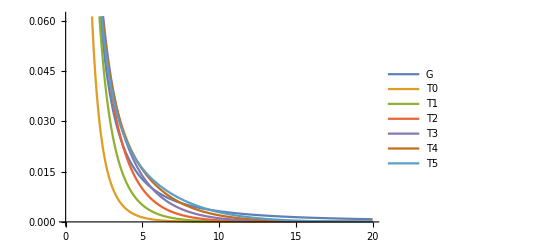

```mathematica
Plot[Evaluate@({G,T}/.d->0.1),{k,0,20},PlotLegends->{"G","T0","T1","T2","T3","T4","T5"}]
```

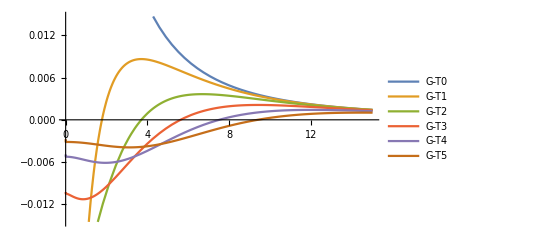

```mathematica
Plot[Evaluate@(G-T/.d->0.1),{k,0,15},PlotLegends->{"G-T0","G-T1","G-T2","G-T3","G-T4","G-T5"}]
```